10

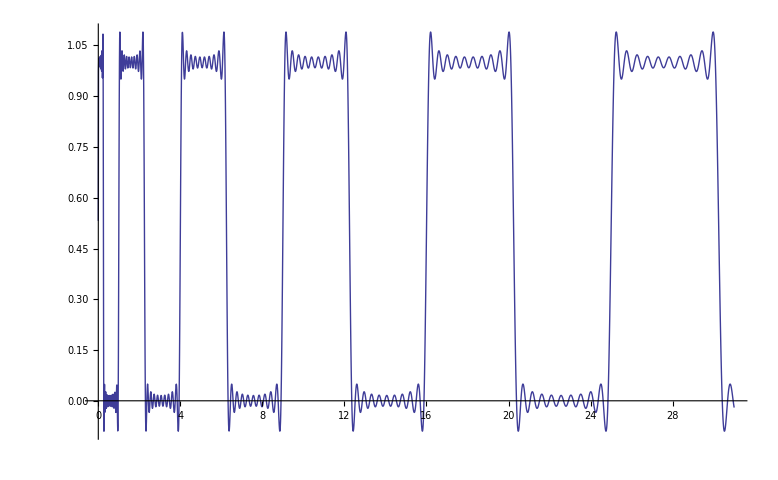

```mathematica
n = 10
f[t_]:=Sum[2Sin[2Pi*(2k-1)*√t]/((2k-1)*Pi),{k,1,n}]
Plot[1/2+ f[t],{t,0,31}]
```

```mathematica
Sum[2Sin[2Pi*√t]/Pi+2Sin[2Pi*3 √t]/(3*Pi)+2Sin[2Pi*5 √t]/(5*Pi)+2Sin[2Pi*7 √t]/(7*Pi)+2Sin[2Pi*9 √t]/(9*Pi)+2Sin[2Pi*11 √t]/(11*Pi) + 2Sin[2Pi*13 √t]/(13*Pi)
```

```mathematica
fo[x_]:=Sum[2Sin[2Pi*k*√t]/Pi,{k,1,10}]
```

```mathematica
N[Sum[MoebiusMu[n]*Cos[2Pi*n],{n,1,500000}]/500000]
```

```mathematica
N[Log[900]]
```

6.80239

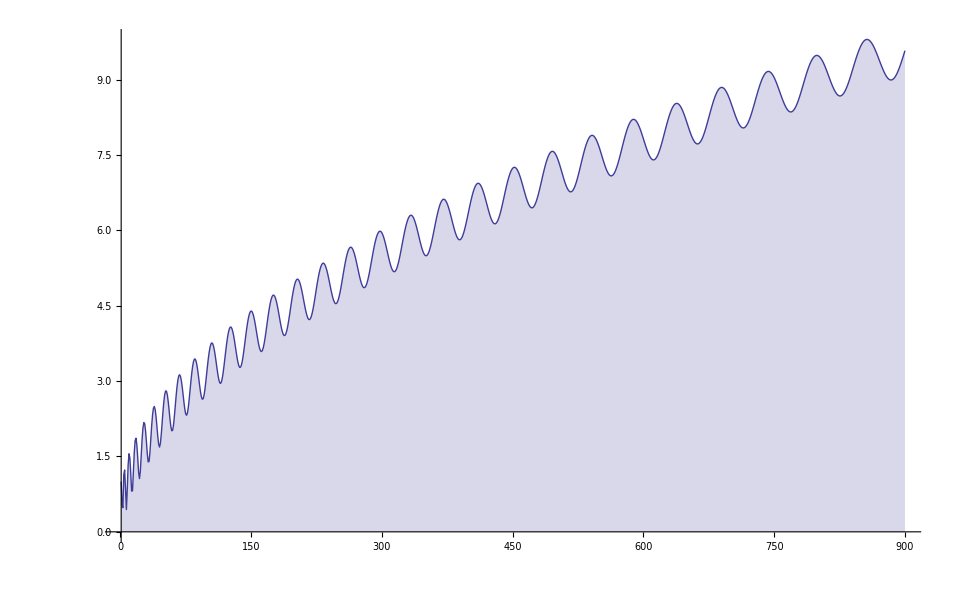

```mathematica
f[n_]:=Abs[Sum[Exp[2Pi*I*(k^{0.5})],{k,1,n}]]
DiscretePlot[f[m],{m,1,900}]
```

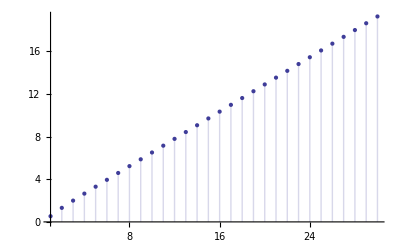

```mathematica
g[n_]:=Abs[Sum[Exp[2Pi*I*(k^{0.5})],{k,n^2,n^2+n}]]
DiscretePlot[g[m],{m,1,30}]
```

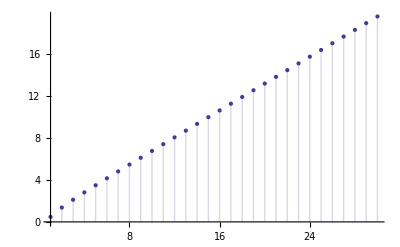

```mathematica
h[n_]:=Abs[Sum[Exp[2Pi*I*(k^{0.5})],{k,n^2+n,(n+1)^2}]]
DiscretePlot[h[m],{m,1,30}]
```

```mathematica
Sqrt''[p*x]
```

-1/(4 (p x)^(3/2))